```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
descdat=ReadList[StringJoin[descDir,seperator,"desc.dat"],{Word,Word,Word,Number,Number,Number,Number,Word}];
Print["CleanCounts: Runs in the list, runNum = ",runnum=descdat[[{-1},4]]]
Print["CleanCounts: Runs in the list, dimNum = ",dimNum=Dimensions[runnum][[1]]];
descdatsens={178.669,219.010,238.976,279.707,281.276,123.572,123.092,124.146,120.273,109.991,88.5941,132.491,132.613,132.471,85.1321,308.688,111.071,112.484,111.323,111.098,108.799,107.874,106.636,105.16,103.476,101.681,98.3486,97.9902,91.7394,95.3069,91.3713,89.1847,85.585,81.3638,76.464,70.7656,62.9919,55.2666,170.993,0,240.262}*363/439;
descdat2=MapThread[Append,{descdat,descdatsens}];
Export[StringJoin[descDir,seperator,"desc2.dat"],descdat2];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

CleanCounts: Runs in the list, runNum = {13146}

CleanCounts: Runs in the list, dimNum = 1

```mathematica
ptmain={};
ptmain180={};
ptmain380={};
ptts={};
ptall={};
maincou=0;
allcou=0;
For[i=1,i≤Dimensions[descdat2][[1]],i++,
If[descdat2[[i]][[5]]>100,
ptmain=AppendTo[ptmain,{N[descdat2[[i]][[5]]*(descdat2[[i]][[7]]+120)/3600],descdat2[[i]][[9]]}];ptall=AppendTo[ptall,{N[descdat2[[i]][[5]]*(descdat2[[i]][[7]]+120)/3600],descdat2[[i]][[9]]}];
If[descdat2[[i]][[7]]==180,
ptmain180=AppendTo[ptmain180,{N[descdat2[[i]][[5]]*(descdat2[[i]][[7]]+120)/3600],descdat2[[i]][[9]]}];,ptmain380=AppendTo[ptmain380,{N[descdat2[[i]][[5]]*(descdat2[[i]][[7]]+120)/3600],descdat2[[i]][[9]]}];
];,
ptts=AppendTo[ptts,{N[descdat2[[i]][[5]]*(descdat2[[i]][[7]]+120)/3600],descdat2[[i]][[9]]}];ptall=AppendTo[ptall,{N[descdat2[[i]][[5]]*(descdat2[[i]][[7]]+120)/3600],descdat2[[i]][[9]]}];
];
];
Dimensions[ptmain]
Dimensions[ptmain180]
Dimensions[ptmain380]
Dimensions[ptts]
Dimensions[ptall]
```

{8,2}

{5,2}

{3,2}

{33,2}

{41,2}

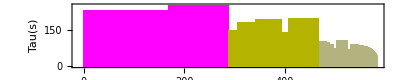

```mathematica
RectangleChart[<|{"380s"->ptmain380,"180s"->ptmain180,"ts-scans"->ptts}|>,AxesLabel->Automatic,Frame->True,FrameLabel->{"Time (h)","Tau(s)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{26,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},AspectRatio->1/5,
ChartStyle->{{RGBColor[1,0,1],RGBColor[.7,.7,0],RGBColor[.7,.7,.5],RGBColor[.7,.7,.7],RGBColor[.7,.7,.9],RGBColor[.5,0,.5],RGBColor[0,.7,.7],RGBColor[.1,.9,.1],RGBColor[0,.3,0],RGBColor[.9,.7,.7],RGBColor[1,0,0]},None},BarSpacing->1]
```

FittedModel[-3.92206+75.939 xx^0.25]

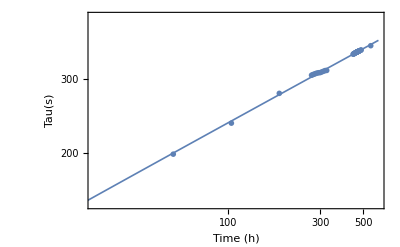

```mathematica
ptlst=Table[{0,0},{k,1,Dimensions[ptall][[1]]}];
For[i=1,i≤Dimensions[ptall][[1]],i++,
ptlst[[i]]={Total[ptall[[1;;i,1]]],(Total[ptall[[1;;i,2]]^4])^(.25)};
]
nlm=NonlinearModelFit[ptlst,aa+bb xx^.25,{{aa,1},{bb,-1}},xx]
Show[{
ListLogLogPlot[ptlst,Frame->True,FrameLabel->{"Time (h)","Tau(s)"},PlotRange->{{20,599},{150,425}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{32,Black,Thick},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotMarkers->{Red,Medium},Ticks->{Table[{i,i,0},{i,10,599,300}],Automatic}],
LogLogPlot[nlm[x],{x,0,600},PlotStyle->Thickness[.003],PlotRange->{{10,599},{150,499}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200}]
}]
```

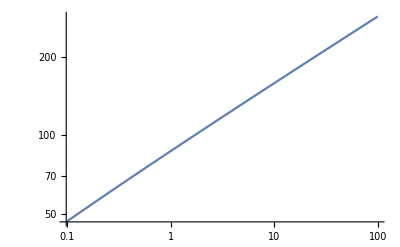

```mathematica
LogLogPlot[nlm[x],{x,0,100}]
```